# Universal Estimator

## Parameter range adjustment

For convenience, we want to work with parameters  ∈ (0,1) and map them to the parameters in the original range.
For that, we can use the Logistic function and its Logit inverse.

#### The Logistic function

The standard Logistic function, σ(x), defined in (-∞, ∞) and yields values in (0,1):

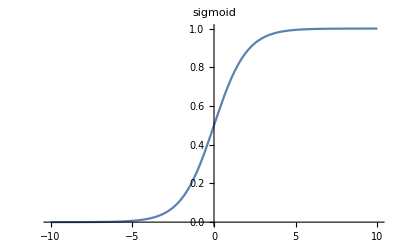

```mathematica
Sigmoid[x_]:=1/(1+ⅇ^-x)
Plot[Sigmoid[x], {x, -10, +10}, PlotLabel->HoldForm[sigmoid]]
```

#### The Logit function

The Logit  is the inverse of the Logistic function σ(x), defined in (0,1) and yields values in (-∞, ∞).
Let’s find the inverse:
σ(x) = y =  1/(1+e^-x) ⇒  1+e^-x = 1/y  ⇒  e^-x = 1/y-1=(1-y)/y  ⇒  log(e^-x)=log((1-y)/y)  ⇒  -x = log((1-y)/y)  ⇒  x = log(y/(1-y)) = σ^-1(x)

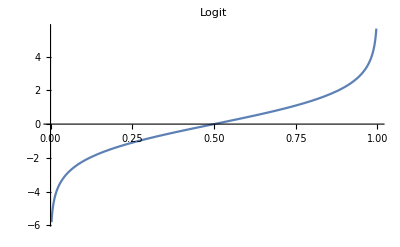

```mathematica
Logit[x_]:= Log[x/(1-x)]
Plot[Logit[x], {x, 0, 1}, PlotLabel->HoldForm[Logit]]
```

### Range Adjuster

We define an Adjuster function which returns another function that maps a parameter in the range  (0,1) to the range  (low, high) of the original distribution.
We can use the Logistic function and its Logit inverse as follows:
Let
	h(t) = Logit(t) , t ∈ (0,1)
Than
	h^-1(d) = Sigmoid(d) , d ∈ (-∞, ∞)

```mathematica
Adjuster[low_, high_]:=With[{LOW=Sigmoid[low],HIGH=Sigmoid[high]}, Function[{t},Logit[LOW+t(HIGH-LOW)]]]
```

### Test Adjuster

For example, we can create an Adjuster for the range [2,5] and call it with values ∈ [0,1]

```mathematica
adj=Adjuster[2, 5];
Print[adj[0.01]];
```

2.01076

```mathematica
Print[adj[0.99]];
```

4.84348

Plot of the adjuster output in the range [0,1]

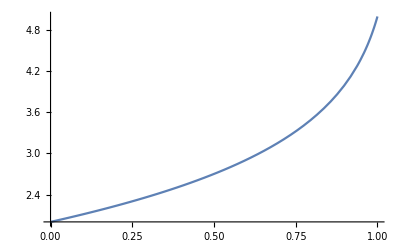

```mathematica
Print[Plot[adj[x], {x,0,1}]]
```

## Generate data

Arguments:

nSamples: number of samples to generate

M: number of observations in each sample

f: the function to generate samples

ranges: an array [d X 2] of parameter ranges (e.g. for 2 parameters: [[0, 10], [0, ∞]])

bins: number of bins in histograms (default: max[samples]+1)

Returns:

a table of associations: histogram -> params (over all samples)

```mathematica
GenerateData[nSamples_, M_, f_, ranges_, bins_:-1]:= 
Module[{nParams, adjusters, params,samples, nbins},

(*number of parameters*)
nParams=Dimensions[ranges][[1]];

(*generate an adapter for each parameter range*)
adjusters=Table[Adjuster[ranges[[i,1]],ranges[[i,2]]],{i,1,nParams}];

(*generate N parameters cube in the range (0,1)*)
params=Table[adjusters[[j]][RandomReal[{0,1}]],{i,1,nSamples},{j,1,nParams}];

(*output*)
(*generate N samples from the parameters*)
samples=Table[f[params[[i]],M],{i,1,nSamples}];

(*create a histogram from each sample*)
nbins=If [bins>0,bins,Max[samples]+1];
h[x_]:=HistogramList[x, {0,nbins,1}][[2]];

(*output*)
Table[h@samples[[i]]-> params[[i]], {i, 1, nSamples}]
]
```

Test GenerateData

```mathematica
YuleSimon[{α_,β_}, M_]:=RandomVariate[WaringYuleDistribution[α,β],M];
YuleSimonRanges = {{2,3},{0,10}};

Print[];
Print["YuleSimon"];
YuleSimonData = GenerateData[5,10,YuleSimon, YuleSimonRanges];
Print[YuleSimonData//TableForm];
```

YuleSimon

{4,4,0,0,0,1,0,0,0,0,1,0,0,0,0}→{2.97032,2.14308}
{7,1,1,0,0,0,0,0,0,0,0,0,0,0,1}→{2.20013,0.286147}
{6,4,0,0,0,0,0,0,0,0,0,0,0,0,0}→{2.16567,2.43524}
{8,0,1,0,0,0,0,0,0,0,1,0,0,0,0}→{2.68065,0.93172}
{10,0,0,0,0,0,0,0,0,0,0,0,0,0,0}→{2.26979,0.11557}

## DNN

```mathematica
CreateNet[bins_, nParams_]:=( 
NetChain[{
LinearLayer[bins], 
(*BatchNormalizationLayer[],*)
ElementwiseLayer[Ramp], 
(*DropoutLayer[0.2],*)
LinearLayer[bins], 
(*BatchNormalizationLayer[],*)
ElementwiseLayer[Ramp], 
(*DropoutLayer[0.2],*)
LinearLayer[nParams]},
"Input"->bins, 
"Output" -> nParams]
)

M = 256;
nSamples = 1000;
trainSet=GenerateData[nSamples,M,YuleSimon, YuleSimonRanges];
bins = Length@trainSet[[1]][[1]];
valSet=GenerateData[nSamples/4,M,YuleSimon, YuleSimonRanges, bins];
nParams=Dimensions[YuleSimonRanges][[1]];
net = NetInitialize@CreateNet[bins, nParams];
(*Print[NetGraph[net]];*)
trained=NetTrain[net,trainSet,Method->"ADAM", 
ValidationSet->valSet, 
LossFunction->MeanAbsoluteLossLayer[]];
(*evaluate*)
trained[HistogramList[YuleSimon[{2.1,0.5},M],{0,bins,1}][[2]]]
```

{2.15541,0.4809}

## Experiments

Define some longtail distributions.
Run an experiment for each longtail distribution.

Assuming 2 parameters for the distribution:

Generate learning samples (train/val) for the given parameters ranges (using GenerateData defined above).

Train a NN model for predicting the parameters corresponding to each sample.

Create a 2-dimensional parameters mesh on the unit square, with 0.1 resolution (i.e: 0.1, 0.2, ... , 0.9)
The mesh is a cube of size 9^2 (81 cell matrix), each containing pair of parameter values (t_1,t_2) ∈ [0.1,...,0.9]

At each mesh point:

Run several trials. At each trial:

Create test data (a histogram of a sample generated at that mesh point)

Predict the parameters at the mesh point, averaging the prediction error.

Compute the Cramer-Raw bound for the mesh point.

Record the relation  (prediction error)/(Cramer-Raw bound)

Plot a surface of the relation above at each mesh point, hopefully showing a value around 2 at each point.

#### Define longtail distributions

```mathematica
(*Sample M observations from the Yule distribution with shape parameters α and β.*)
YuleSimonRV[{α_,β_}, M_]:=RandomVariate[WaringYuleDistribution[α,β],M];

(*Sample M observations from the PowerLaw distribution with domain parameter k and shape parameter a.*)
PowerLawRV[{k_,a_}, M_]:=RandomVariate[PowerDistribution[k,a],M];

(*Log-Normal*)
LogNormalRV[{μ_,σ_}, M_]:=RandomVariate[LogNormalDistribution[μ,σ],M];
```

#### Define an Association for each distribution

```mathematica
distributions = Association[
"yulesimon" -> Association["dist"->YuleSimonRV, "ranges"->{{2,3},{0,10}}, "M"->256],
"powerlaw" -> Association["dist"->PowerLawRV, "ranges"->{{1,10},{0,10}}, "M"->256],
"lognormal" -> Association["dist"->LogNormalRV, "ranges"->{{1,3},{0,5}}, "M"->256]
];
```

```mathematica
(*test association*)
dist = distributions["yulesimon"];
f = dist["dist"];
ranges = dist["ranges"];
M = dist["M"];
f[ranges[[1]], M]
```

{5,1,0,0,0,0,0,1,0,0,0,4,0,0,4,3,2,2,0,2,0,5,2,13,1,0,0,1,0,21,1,1,0,0,1,8,22,2,0,0,0,1,0,1,4,5,6,0,1,0,0,21,68,0,3,0,0,0,14,0,0,7,0,9,0,0,0,1,0,1,6,23,0,0,5,0,0,4,1,0,0,2,1,1,3,0,2,6,13,0,5,1,1,12,1,2,3,0,0,4,4,0,5,0,4,1,0,3,0,0,0,0,0,4,2,0,17,0,0,36,2,2,1,0,1,2,1,5,0,2,4,1,3,6,0,25,0,0,0,2,0,5,1,5,2,0,7,2,4,0,6,0,5,2,5,0,2,0,1,3,0,4,5,3,1,1,11,1,0,1,0,2,0,0,0,0,0,24,2,0,9,2,3,0,0,3,8,1,0,1,0,0,0,2,0,0,0,0,0,0,2,5,2,0,1,1,0,1,0,0,0,0,0,3,0,1,1,6,1,0,38,6,9,0,0,1,3,1,1,3,0,0,0,0,4,0,0,1,2,0,1,1,4,5,1,1,16,10,7,0,0,0,0,6,0,7}

### Run the experiments

An experiment for a single distribution

```mathematica
RunExperiment[distributions_, distname_]:=
Module[{dist, f, ranges, M, nSamples, trainSet, bins, nParams, valSet, net, model, adjuster1, adjuster2, mesh},

(*get definitions for the distribution specified by distname*)
dist = distributions[distname];
f = dist["dist"];
ranges = dist["ranges"];
M = dist["M"];

(*Generate learning samples (train/val) for the parameters ranges (using GenerateData defined above).*)
nSamples = 100;(*lilo: 1000*)
trainSet=GenerateData[nSamples,M,f, ranges];
(*we need the same number of bins for the validation set*)
bins = Length@trainSet[[1]][[1]];
valSet=GenerateData[nSamples/4,M,f, ranges, bins];

(*Train a NN model for predicting the parameters corresponding to each sample.*)
nParams=Dimensions[ranges][[1]];
net = NetInitialize@CreateNet[bins, nParams];
model=NetTrain[
net,trainSet,
Method->"ADAM", 
ValidationSet->valSet, 
LossFunction->MeanAbsoluteLossLayer[]];

(*Create an adjuster for each parameter*)
adjuster1=Adjuster[ranges[[1,1]],ranges[[1,2]]];
adjuster2=Adjuster[ranges[[2,1]],ranges[[2,2]]];

(*Create a 2-dimensional parameters mesh on the unit square*)
mesh = Table[{adjuster1[i],adjuster2[j]},{i,0.1,0.9,0.1 },{j,0.1,0.9,0.1 }];

(*output*)
(*Process each mesh point*)
Table[EvaluateMeshPoint[mesh[[i,j]], model, f],{i,1,9 },{j,1,9 }]
];

EvaluateMeshPoint[model_, f_, params_, M_, bins_]:= 
Module[{sample, histogram, cycles, predicted, error},
(*Run n cycles*)
error=0;
cycles=3;
For[i=0; , i < cycles, i+=1,
(*Create a histogram from a sample generated using the given parameters)*)
sample=f[params,M];
histogram = HistogramList[sample, {0,bins,1}][[2]];

(*Predict the parameters, averaging the prediction absolute error.*)
predicted = model[histogram];
error += Abs[predicted - params];

(*Print["lilo ------------------------params: ", params];
Print["lilo ------------------------prediced: ", predicted];
Print["lilo ------------------------error: ", error]*)
];

(*avg the errors across all parameters*)
error=Mean[error /cycles];

(*Compute the Cramer-Raw bound for the mesh point.*)
(*Return the relation(prediction error)/(Cramer-Raw bound)*)
error/CramerRawBound[params, M]
];

CramerRawBound[params_, M_]:=Module[{},
(*TODO*)
0.2
];

RunExperiment[distributions, "yulesimon"]
```

{{{2.07022,0.200652},{2.07022,0.405427},{2.07022,0.618979},{2.07022,0.847211},{2.07022,1.09849},{2.07022,1.38612},{2.07022,1.73435},{2.07022,2.19682},{2.07022,2.94358}},{{2.14449,0.200652},{2.14449,0.405427},{2.14449,0.618979},{2.14449,0.847211},{2.14449,1.09849},{2.14449,1.38612},{2.14449,1.73435},{2.14449,2.19682},{2.14449,2.94358}},{{2.22339,0.200652},{2.22339,0.405427},{2.22339,0.618979},{2.22339,0.847211},{2.22339,1.09849},{2.22339,1.38612},{2.22339,1.73435},{2.22339,2.19682},{2.22339,2.94358}},{{2.30764,0.200652},{2.30764,0.405427},{2.30764,0.618979},{2.30764,0.847211},{2.30764,1.09849},{2.30764,1.38612},{2.30764,1.73435},{2.30764,2.19682},{2.30764,2.94358}},{{2.39814,0.200652},{2.39814,0.405427},{2.39814,0.618979},{2.39814,0.847211},{2.39814,1.09849},{2.39814,1.38612},{2.39814,1.73435},{2.39814,2.19682},{2.39814,2.94358}},{{2.49603,0.200652},{2.49603,0.405427},{2.49603,0.618979},{2.49603,0.847211},{2.49603,1.09849},{2.49603,1.38612},{2.49603,1.73435},{2.49603,2.19682},{2.49603,2.94358}},{{2.60279,0.200652},{2.60279,0.405427},{2.60279,0.618979},{2.60279,0.847211},{2.60279,1.09849},{2.60279,1.38612},{2.60279,1.73435},{2.60279,2.19682},{2.60279,2.94358}},{{2.72038,0.200652},{2.72038,0.405427},{2.72038,0.618979},{2.72038,0.847211},{2.72038,1.09849},{2.72038,1.38612},{2.72038,1.73435},{2.72038,2.19682},{2.72038,2.94358}},{{2.8515,0.200652},{2.8515,0.405427},{2.8515,0.618979},{2.8515,0.847211},{2.8515,1.09849},{2.8515,1.38612},{2.8515,1.73435},{2.8515,2.19682},{2.8515,2.94358}}}